```mathematica
ClearAll[Evaluate[Context[]<>"*"]]
```

```mathematica
Import["/home/luca/Desktop/BusinessAnalytics/Homework2/Q.csv"];
Q=ArrayReshape[%,{3,3,101,101}];
V=Table[Min[Q[[All,s,i,j]]],{s,3},{i,101},{j,101}];
μ=Table[Ordering[Q[[All,s,i,j]],1][[1]],{s,3},{i,101},{j,101}];
Dimensions[V]
Dimensions[μ]
```

{3,101,101}

{3,101,101}

```mathematica
Table[MatrixPlot[μ[[s]]-1,PlotLegends->Automatic,PlotRange->{0,3},ImageSize->300],{s,3}]//Row
```

-Graphics--Graphics--Graphics-

```mathematica
ListPlot3D[V[[2]],PlotRange->All]
```

-Graphics3D-

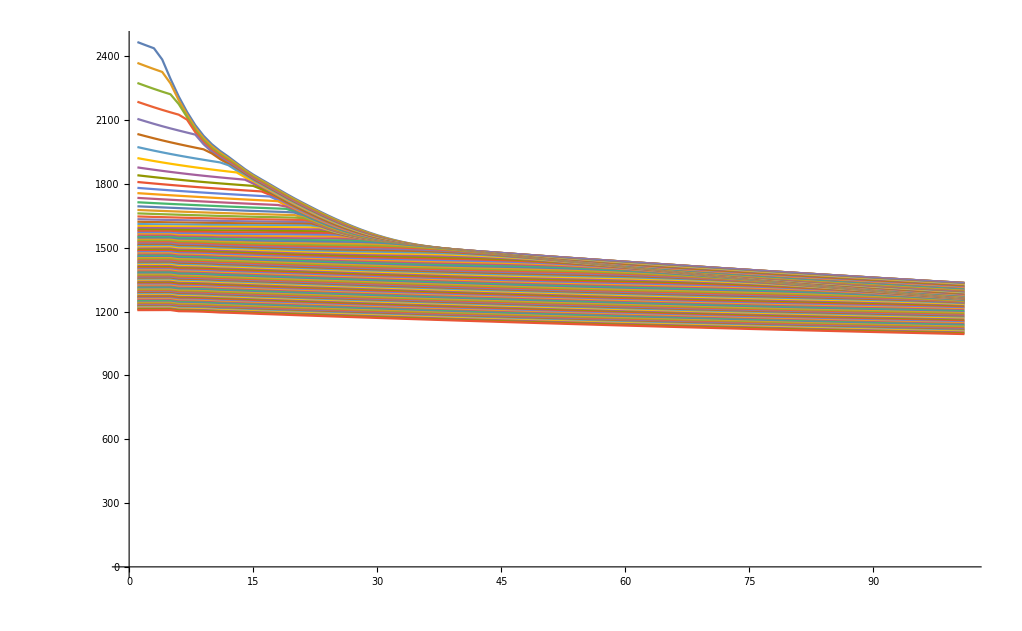

```mathematica
ListLinePlot[V[[1]],PlotRange->All]
```

```mathematica
Plot3D[Exp[-Max[i,j]/10^2],{i,0,100},{j,0,100},PlotRange->All]
```

-Graphics3D-

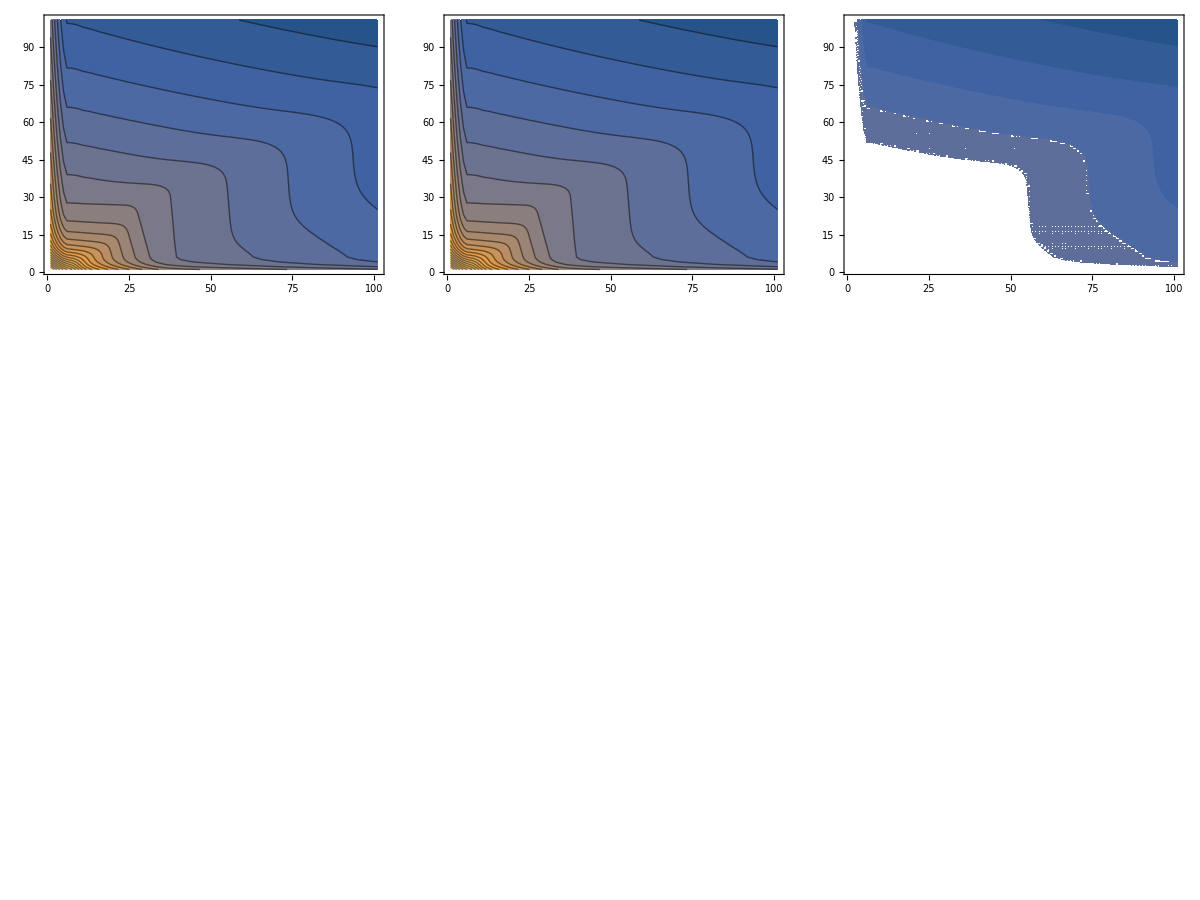

-Graphics3D-

```mathematica
Table[ListContourPlot[Q[[a,s]],PlotRange->All,Contours->25,ImageSize->300],{a,1,3},{s,1,3}]//TableForm
```

```mathematica
33^4
```

1185921

```mathematica
idx=Join[Range[25],Range[26,101,10]]
Dimensions[idx]
Dimensions@Flatten@Table[Exp[((i-ic)^2+(j-jc)^2)/100],{ic,idx},{jc,idx}]
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,36,46,56,66,76,86,96}

{33}

{1089}

162.7497132938839

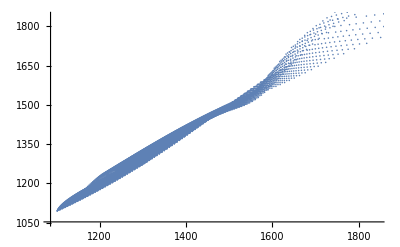

```mathematica
lm=LinearModelFit[
Flatten[Table[{i,j,V[[1,i,j]]},{i,101},{j,101}],1],
{1,i,j,i^2,j^2,i*j,1/(i+j),1/(i^2+j^2+1),Exp[-(i^2+j^2)/100],If[i+j<10,i^2+j^2,0],Exp[-Max[i,j]/100]},
{i,j},IncludeConstantBasis->False
];
(*relerrs=Sort@Flatten@Table[RealAbs[V[[s,i,j]]-lm[s,i,j]]/RealAbs[V[[s,i,j]]],{s,3},{i,101},{j,101}];
ListLinePlot[relerrs,PlotRange->All]*)
relerrs=RealAbs/@lm["FitResiduals"];
Max[relerrs]
ListPlot[Flatten[Table[{lm[i,j],V[[1,i,j]]},{i,101},{j,101}],1]]
(*ListPlot3D[ArrayReshape[lm["FitResiduals"],{101,101}],PlotRange->All]
lm["AdjustedRSquared"]
lm["ParameterTable"]*)
```

PredictorFunction[…]

PredictorMeasurementsObject[…]

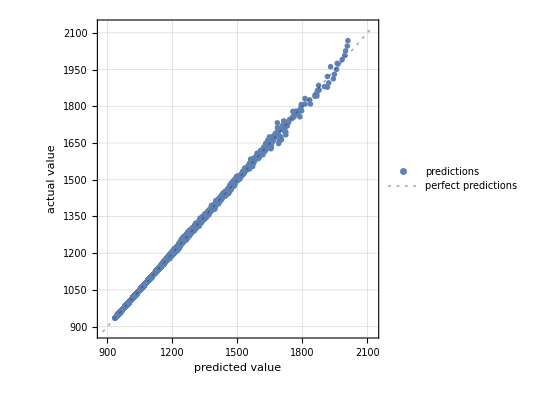

57.6193

```mathematica
p=Predict[Flatten[Table[{i,j}->V[[2,i,j]],{i,idx},{j,idx}],1],Method->"GradientBoostedTrees",PerformanceGoal->{"Quality","DirectTraining"}]
pm=PredictorMeasurements[p,Flatten[Table[{i,j}->V[[2,i,j]],{i,1,101},{j,1,101}],1]]
pm["ComparisonPlot"]
Max[RealAbs[pm["Residuals"]]]
```

PredictorFunction[…]

PredictorMeasurementsObject[…]

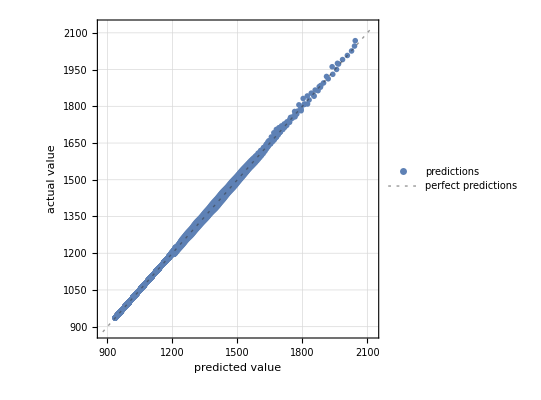

Values::invrl: The argument Missing[KeyAbsent,Experiments] is not a valid Association or a list of rules.

ListPlot::prng: Value of option PlotRange -> {{Automatic,Missing[KeyAbsent,MaxTrainingSize]},Automatic} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

Values::invrl: The argument Missing[KeyAbsent,Experiments] is not a valid Association or a list of rules.

General::stop: Further output of Values::invrl will be suppressed during this calculation.

ListPlot::prng: Value of option PlotRange -> {{Automatic,Missing[KeyAbsent,MaxTrainingSize]},Automatic} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

General::stop: Further output of ListPlot::prng will be suppressed during this calculation.

Predictor information
Data type | {Numerical,Numerical}
Method | GaussianProcess
Single evaluation time | 87.9 ms/example
Batch evaluation speed | 97. examples/s
Model memory | 832. MB
Training examples used | 10201 examples
Training time | 7 3
 |

28.0482

```mathematica
idx=Range[101];
p=Predict[Flatten[Table[{i,j}->V[[2,i,j]],{i,idx},{j,idx}],1],Method->{"GaussianProcess",AssumeDeterministic->True},PerformanceGoal->{"Quality","DirectTraining"}]
pm=PredictorMeasurements[p,Flatten[Table[{i,j}->V[[2,i,j]],{i,1,101},{j,1,101}],1]]
pm["ComparisonPlot"]
Information[p]
Max[RealAbs[pm["Residuals"]]]
```

```mathematica
Information[p,"InternalParameters"]
```

{SquaredExponential→<|NumericalLengthScale→0.187205,SignalVariance→0.146172|>}

```mathematica
Information[p,"InternalParameters"]
```

{SquaredExponential→<|NumericalLengthScale→0.132038,SignalVariance→6.55956|>,WN→<|NoiseVariance→0.00133083|>}

```mathematica
Spline
```

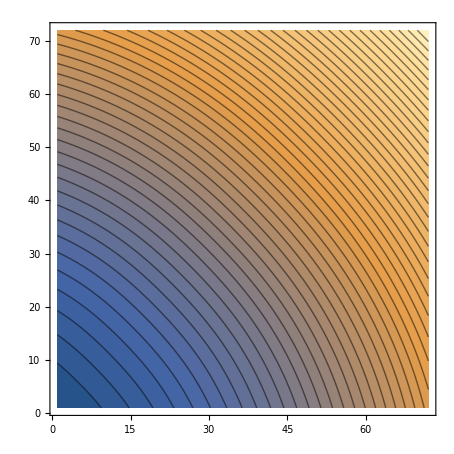

-Graphics3D-

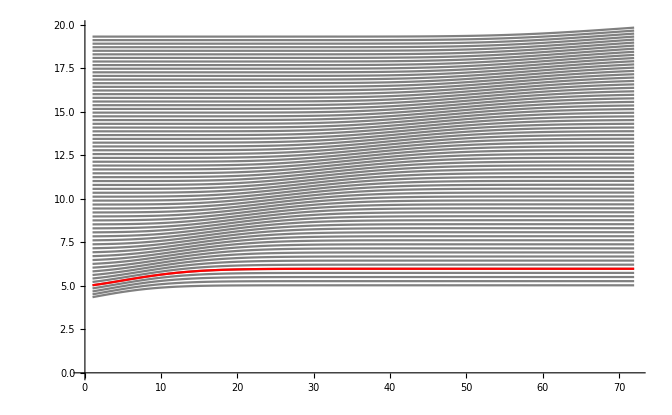

```mathematica
data=Import["/home/luca/Desktop/BusinessAnalytics/Homework2/V.txt","CSV"];
ListContourPlot[data[[30;;,30;;]],Contours->50]
ListPlot3D[data[[30;;,30;;]]]
Show[
ListLinePlot[Differences[data[[30;;,30;;]]],PlotRange->All,PlotStyle->Gray],
ListLinePlot[Differences[data[[30;;,30;;]]][[5]],PlotRange->All,PlotStyle->Red]
]
```

```mathematica
derivate=Differences[data][[20;;;;4]];
mds=Table[NonlinearModelFit[deriv,a+b  Erf[-c(x+d)/100],{a,{b,3},{c,4.5},d},x,Method->"Newton"],{deriv,derivate}];
```

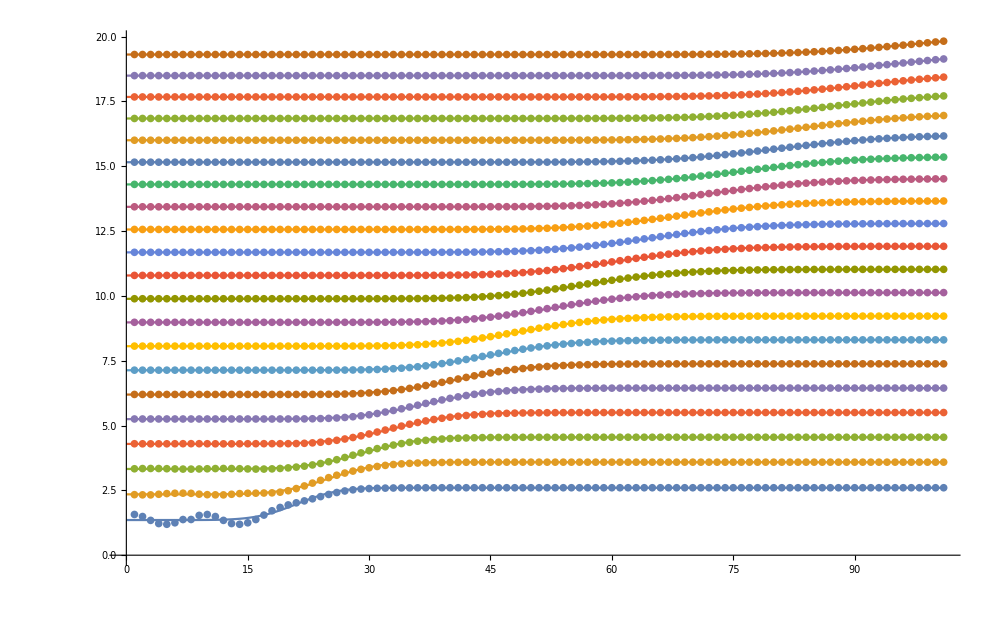

```mathematica
Show[ListPlot[derivate],Plot[Evaluate@Table[m[x],{m,mds}],{x,0,Length@data},PlotRange->All],ImageSize->1000]
```

```mathematica
Table[{i,-c*d/100,-c/100}/.mds[[i]]["BestFitParameters"],{i,1,Length@mds}]//Column
```

{1,3.699496214541,-0.17544525334524}
{2,3.6528848241608,-0.145463026838201}
{3,3.6720664083551,-0.126082681932412}
{4,3.73519032503914,-0.112817435233818}
{5,3.82510578047983,-0.103114830170901}
{6,3.92672816635879,-0.0955746850612198}
{7,4.02960962222552,-0.089413083260756}
{8,4.13859846173172,-0.0843729787429691}
{9,4.25132705824601,-0.0801642654698086}
{10,4.36498547423658,-0.0765650122319732}
{11,4.48031008221954,-0.0734753891073888}
{12,4.60216460701579,-0.0708711440235203}
{13,4.72467150726872,-0.0685986644174983}
{14,4.86120432889363,-0.0667844741384893}
{15,5.00449610241781,-0.0652782492563554}
{16,5.16573415666574,-0.0641805407232055}
{17,5.32816645154571,-0.0632357594896664}
{18,5.50916445203249,-0.0626583126737941}
{19,5.68707515741293,-0.0621311604091189}
{20,5.86066601885863,-0.0616384371511753}
{21,6.05396126494778,-0.061493600146232}

| Estimate | Standard Error | Confidence Interval
1 | 2009.51413872277565 | 0.459015625532247 | {2008.61437779724893,2010.41389964830237}
x | -2.56987456785123386 | 0.0128674395131131 | {-2.5950972806337302,-2.5446518550687376}
y | -2.56987526563570029 | 0.0128674395131131 | {-2.5950979784181966,-2.544652552853204}
x^2 | 0.107897884907261876 | 0.000110276636836288 | {0.10768172100497916,0.10811404880954459}
y^2 | 0.107897889036568478 | 0.000110276636836288 | {0.10768172513428576,0.10811405293885119}
x y | 0.0130874355360098978 | 0.0000998485208132657 | {0.012891712792595129,0.013283158279424667}
1/(1+x^2+y^2) | 2985.21331677629388 | 17.8785425625983 | {2950.1678562115486,3020.2587773410391}

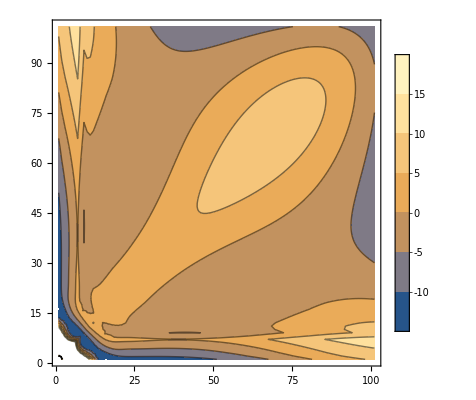

{-414.92681909711651,155.7713961450945}

```mathematica
datainla=Table[{i,j,data[[i,j]]},{i,1,Length@data},{j,1,Length@data}];
mm=LinearModelFit[Flatten[datainla,1],{1,x,y,x^2,y^2,x*y,1/(x^2+y^2+1)(*x y,1/x,1/y,1/(x y),x^3*)},{x,y}];
mm["ParameterConfidenceIntervalTable"]
ListContourPlot[ArrayReshape[mm["FitResiduals"],{Length@datainla,Length@datainla}],PlotLegends->Automatic]
MinMax@mm["FitResiduals"]
```

```mathematica
Fdata=FourierDCT[data];
FFdata=FourierDCT[Fdata*Table[If[i==1∨j==1,1,0],{i,1,Length@data},{j,1,Length@data}],3];
```

```mathematica
Fdata[[;;10,;;10]]//MatrixForm
```

(255320.85969649 | -18698.51207488 | 5728.62816669 | -1909.66365861 | 1481.67582057 | -648.63997411 | 685.31189703 | -311.12076079 | 398.33500386 | -179.60471829
-18698.51264124 | 675.57373571 | 117.54484727 | 96.41287513 | 89.17228175 | 86.42898776 | 78.79648793 | 74.83419946 | 67.3109544 | 62.41240549
5728.62789181 | 117.54548914 | 226.84234866 | 102.9419519 | 90.64000701 | 83.01007242 | 79.29394422 | 71.84736877 | 67.15725021 | 60.00676435
-1909.66376136 | 96.41231763 | 102.9414188 | 140.2657694 | 93.07289819 | 83.23386521 | 75.56284754 | 70.91519012 | 63.81006224 | 58.66697231
1481.67617596 | 89.17251848 | 90.64006866 | 93.07311558 | 105.9968189 | 83.09513986 | 74.45810273 | 66.97690034 | 61.70011728 | 55.0343337
-648.64023124 | 86.42921934 | 83.01012192 | 83.23376892 | 83.09504396 | 85.91903118 | 72.52111425 | 64.73026456 | 57.61077431 | 52.079599
685.31176614 | 78.79642687 | 79.29396456 | 75.56290983 | 74.45811893 | 72.52120697 | 70.84825519 | 61.57760156 | 54.52360785 | 47.91381669
-311.12044291 | 74.83410162 | 71.84724486 | 70.91503161 | 66.9769507 | 64.73001763 | 61.57761916 | 57.93091512 | 50.65746419 | 44.32840642
398.33452686 | 67.31083856 | 67.15726989 | 63.81032956 | 61.70026978 | 57.61080491 | 54.523553 | 50.65743084 | 46.28010712 | 40.18436133
-179.60487538 | 62.41241597 | 60.00661405 | 58.66695133 | 55.03418129 | 52.07964546 | 47.91386306 | 44.32853647 | 40.18411818 | 35.74634386)

```mathematica
FFdata=8*10^4FourierDCT[Evaluate@Table[
Fdata[[x,y]]*If[(x==1)∨(y==1)∨(Abs[x-y]<2),1,0]
,{x,1,Length@data},{y,1,Length@data}],3];
ListPlot3D[Rescale@data]
ListPlot3D[Rescale@FFdata]
ListPlot3D[Rescale[data]-Rescale[FFdata]]
```

-Graphics3D-

-Graphics3D-

-Graphics3D-

```mathematica
MinMax[Rescale[data][[20;;-5,20;;-5]]-Rescale[FFdata][[20;;-5,20;;-5]]]
```

{0.,0.}

```mathematica
data={{13,8,7,10,13,12,7,6,9,12,15,10,9,12,15,18,13,12,15,18,21,16,15,18,21},{13,12,15,18,21,8,7,10,13,16,7,6,9,12,15,10,9,12,15,18,13,12,15,18,21},{18,13,12,15,18,13,8,7,10,13,12,7,6,9,12,15,10,9,12,15,18,13,12,15,18}}/3;
```

```mathematica
k0={3,4/3,1,2,3};
kA={4/3,1,2,3,4};
Flatten@Table[k0+d,{d,kA}]==data[[1]]
Flatten@Table[kA+d,{d,k0}]==data[[2]]
Flatten@Table[k0+d,{d,k0}]==data[[3]]
```

True

True

True

```mathematica
Flatten@Table[{a,b,c}+Δ,{Δ,{d,e,f}}]
```

{a+d,b+d,c+d,a+e,b+e,c+e,a+f,b+f,c+f}

```mathematica
Flatten@KroneckerProduct[Exp@kA,Exp@k0]==Exp@data[[1]]
Flatten@KroneckerProduct[Exp@k0,Exp@kA]==Exp@data[[2]]
Flatten@KroneckerProduct[Exp@k0,Exp@k0]==Exp@data[[3]]
```

True

True

True

```mathematica
KroneckerProduct[Transpose@{kA},IdentityMatrix[5]]+KroneckerProduct[IdentityMatrix[5],Transpose@{k0}]//MatrixForm
Total[Transpose@%]==data[[1]]
```

(13/3 | 0 | 0 | 0 | 0
4/3 | 4/3 | 0 | 0 | 0
1 | 0 | 4/3 | 0 | 0
2 | 0 | 0 | 4/3 | 0
3 | 0 | 0 | 0 | 4/3
1 | 3 | 0 | 0 | 0
0 | 7/3 | 0 | 0 | 0
0 | 1 | 1 | 0 | 0
0 | 2 | 0 | 1 | 0
0 | 3 | 0 | 0 | 1
2 | 0 | 3 | 0 | 0
0 | 2 | 4/3 | 0 | 0
0 | 0 | 3 | 0 | 0
0 | 0 | 2 | 2 | 0
0 | 0 | 3 | 0 | 2
3 | 0 | 0 | 3 | 0
0 | 3 | 0 | 4/3 | 0
0 | 0 | 3 | 1 | 0
0 | 0 | 0 | 5 | 0
0 | 0 | 0 | 3 | 3
4 | 0 | 0 | 0 | 3
0 | 4 | 0 | 0 | 4/3
0 | 0 | 4 | 0 | 1
0 | 0 | 0 | 4 | 2
0 | 0 | 0 | 0 | 7)

True